# PropertyAssociation

Make a property association

## Definition

```mathematica
ClearAll[PropertyAssociation]
```

```mathematica
PropertyAssociation[input_/;TrueQ[VectorQ[input["Properties"]]]]:=AssociationMap[input[#]&,input["Properties"]]
```

```mathematica
PropertyAssociation::usage="PropertyAssociation[arg] builds a property association for the input arg by finding the value of each of its properties.";
```

## Documentation

### Usage

PropertyAssociation[arg]

builds a property association for the input arg by finding the value of each of its properties.

### Details & Options

All entities support property association but other objects don't.

## Examples

### Basic Examples

This is a chat object:

```mathematica
chat1=ChatObject[]
```

ChatObject[…]

Make a property association:

```mathematica
PropertyAssociation[chat1]
```

<|ChatID→1bae6d31-67d1-406d-92f9-14ae8749dcf9,LLMEvaluator→LLMConfiguration[…],Messages→{},Properties→{ChatID,LLMEvaluator,Messages,Properties,Usage},Usage→0 Tokens|>

```mathematica
chat1[All]
```

Missing[InvalidProperty,All]

This is an assessment function:

```mathematica
AssessmentFunction["dog"]["dog"]
```

AssessmentResultObject[…]

Make a property association:

```mathematica
PropertyAssociation[AssessmentFunction["dog"]["dog"]]
```

<|Score→1,MaxScore→1,MinScore→0,AnswerCorrect→True,GivenAnswer→dog,Explanation→None,Timestamp→Sat 24 Jun 2023 08:54:05GMT-4,AssessmentOptions→{},AnswerComparisonMethod→String|>

Trying to call PropertyAssociation fails:

```mathematica
AssessmentFunction["dog"]["dog"]["PropertyAssociation"]
```

Missing[NotAvailable]

### Scope

Text about additional examples expanding scope (and see other sections for options, applications, etc):

```mathematica
MyFunction[x,y,z]
```

x y z

### Options

### Applications

There are many types of objects with properties:

```mathematica
Names["*Object"]
```

{ActiveClassificationObject,ActivePredictionObject,AssessmentResultObject,AsynchronousTaskObject,AxisObject,BayesianMaximizationObject,BayesianMinimizationObject,BoxObject,CellObject,ChannelObject,ChatObject,ClassifierMeasurementsObject,CloudObject,CompilerEnvironmentObject,ContentObject,CreateManagedObject,DateObject,DeleteObject,DeviceObject,EmbeddingObject,EncryptedObject,EvaluationObject,ExternalObject,ExternalSessionObject,ExternalStorageObject,FormObject,FrontEndObject,IconizedObject,ImportedObject,InitializationObject,InsertionPointObject,JavaObject,KeepJavaObject,KernelObject,LicenseEntitlementObject,LinkObject,LocalObject,MakeJavaObject,ManagedObject,MessageObject,NetExternalObject,NetStateObject,NetTrainResultsObject,NotebookInterfaceObject,NotebookObject,PacletObject,PacletSiteObject,PersistentObject,PredictorMeasurementsObject,ProcessObject,ProofObject,QuestionObject,ReleaseJavaObject,ReleaseObject,RemoteBatchJobObject,RemoteConnectionObject,RemoteKernelObject,ResourceObject,ResourceSubmissionObject,ReturnAsJavaObject,ScheduledTaskObject,SearchIndexObject,SearchResultObject,ServiceObject,SocketObject,SystemCredentialStoreObject,TaskObject,TemplateObject,TestObject,TestReportObject,TestResultObject,TimeObject,UnmanageObject,WebElementObject,WebSessionObject,WebWindowObject,XMLObject,$EvaluationCloudObject}

Train an ActiveClassifcationObject[…] to classify whether a number is greater than 0.5:

```mathematica
aco = ActiveClassification[#>0.5&,RandomReal[{0.1,1.2}]&]
```

ActiveClassificationObject[…]

You can't use PropertyAssociation:

```mathematica
aco["PropertyAssociation"]
```

ActiveClassificationObject::elmntavl: "PropertyAssociation" is not an available property. Possible properties include "OracleFunction", "EvaluationHistory", "Method", "Properties", "LearningCurve", "TrainingHistory", "ClassifierFunction", and "ClassifierMeasurementsObject".

ActiveClassificationObject[…][PropertyAssociation]

Find the property association:

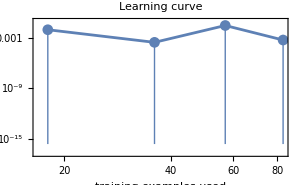
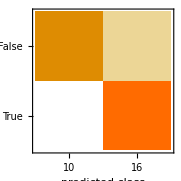
<|OracleFunction→(#1>0.5&),EvaluationHistory→,Method→MaxEntropy,Properties→{OracleFunction,EvaluationHistory,Method,Properties,LearningCurve,TrainingHistory,ClassifierFunction,ClassifierMeasurementsObject},LearningCurve→-Graphics-,TrainingHistory→Dataset[<>],ClassifierFunction→ClassifierFunction[…],ClassifierMeasurementsObject→Classifier Measurements
Classifier method | LogisticRegression
Number of test examples | 26
Accuracy | (98.63.2) %
Accuracy baseline | (71.12.) %
Geometric mean of probabilities | 0.969 ± 0.071
Mean cross entropy | 0.0318 ± 0.073
Single evaluation time | 2.09 ms/example
Batch evaluation speed | 1.09 examples/ms
-Graphics- | |>

```mathematica
PropertyAssociation[aco]
```

Train an ActivePredictionObjectpaclet:ref/ActivePredictionObject[…]  to find the predictor for a nontrivial function in an interval:

```mathematica
apo=ActivePrediction[(#-2)^2&,Interval[{0,5}]]
```

ActivePredictionObject[…]

If you want to get all the properties, apo["PropertyAssociation"] won't work:

```mathematica
apo["PropertyAssociation"]
```

ActivePredictionObject::elmntavl: "PropertyAssociation" is not an available property. Possible properties include "OracleFunction", "EvaluationHistory", "Method", "Properties", "LearningCurve", "TrainingHistory", "PredictorFunction", and "PredictorMeasurementsObject".

ActivePredictionObject[…][PropertyAssociation]

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0 ∞ encountered.

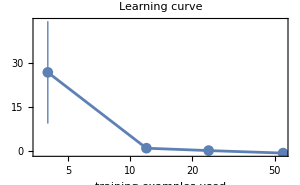
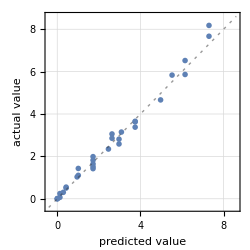
<|OracleFunction→((#1-2)^2&),EvaluationHistory→,Method→MaxEntropy,Properties→{OracleFunction,EvaluationHistory,Method,Properties,LearningCurve,TrainingHistory,PredictorFunction,PredictorMeasurementsObject},LearningCurve→-Graphics-,TrainingHistory→Dataset[<>],PredictorFunction→PredictorFunction[…],PredictorMeasurementsObject→Predictor Measurements
Predictor method | NearestNeighbors
Number of test examples | 31
Standard deviation | 0.251 ± 0.038
Standard deviation baseline | 2.34 ± 0.36
R-squared | 0.989 ± 0.005
Mean cross entropy | 0.285 ± 0.045
Single evaluation time | 1.98 ms/example
Batch evaluation speed | 1.1 examples/ms
-Graphics- | |>

```mathematica
PropertyAssociation[apo]
```

Create an AssessmentResultObjectpaclet:ref/AssessmentResultObject as the output of AssessmentFunctionpaclet:ref/AssessmentFunction:

```mathematica
AssessmentFunction["dog"]["dog"]
```

AssessmentResultObject[…]

You can use All to get the property association in this case:

```mathematica
AssessmentResultObject[…][All]
```

<|Score→1,MaxScore→1,MinScore→0,AnswerCorrect→True,GivenAnswer→dog,Explanation→None,Timestamp→Sat 24 Jun 2023 09:02:17GMT-4,AssessmentOptions→{},AnswerComparisonMethod→String|>

However, you can't use All with the previous two examples:

```mathematica
aco[All]
```

ActiveClassificationObject::elmntavl: All is not an available property. Possible properties include "OracleFunction", "EvaluationHistory", "Method", "Properties", "LearningCurve", "TrainingHistory", "ClassifierFunction", and "ClassifierMeasurementsObject".

ActiveClassificationObject[…][All]

```mathematica
apo[All]
```

ActivePredictionObject::elmntavl: All is not an available property. Possible properties include "OracleFunction", "EvaluationHistory", "Method", "Properties", "LearningCurve", "TrainingHistory", "PredictorFunction", and "PredictorMeasurementsObject".

ActivePredictionObject[…][All]

PropertyAssociation also works:

```mathematica
PropertyAssociation[AssessmentResultObject[…]]
```

<|Score→1,MaxScore→1,MinScore→0,AnswerCorrect→True,GivenAnswer→dog,Explanation→None,Timestamp→Sat 24 Jun 2023 09:03:13GMT-4,AssessmentOptions→{},AnswerComparisonMethod→String|>

Maximize a function over an interval region via BayesianMaximizationpaclet:ref/BayesianMaximization to create a BayesianMaximizationObjectpaclet:ref/BayesianMaximizationObject[…]:

```mathematica
bo =BayesianMaximization[-((#-2)^2+1)&,Interval[{0,5}]]
```

BayesianMaximizationObject[…]

Neither All nor "PropertyAssociation" works:

```mathematica
bo[All]
```

BayesianMaximizationObject::elmntavl: All is not an available property. Possible properties include "MaximumConfiguration", "MaximumValue", "EvaluationHistory", "PredictorFunction", "ObjectiveFunction", "Method", "Properties", and "NextConfiguration".

BayesianMaximizationObject[…][All]

```mathematica
bo["PropertyAssociation"]
```

BayesianMaximizationObject::elmntavl: "PropertyAssociation" is not an available property. Possible properties include "MaximumConfiguration", "MaximumValue", "EvaluationHistory", "PredictorFunction", "ObjectiveFunction", "Method", "Properties", and "NextConfiguration".

BayesianMaximizationObject[…][PropertyAssociation]

To find all the data, use PropertyAssociation:

```mathematica
PropertyAssociation[bo]
```

<|MaximumConfiguration→2.01206,MaximumValue→-1.00761,EvaluationHistory→,PredictorFunction→PredictorFunction[…],ObjectiveFunction→(-((#1-2)^2+1)&),Method→MaxExpectedImprovement,Properties→{MaximumConfiguration,MaximumValue,EvaluationHistory,PredictorFunction,ObjectiveFunction,Method,Properties,NextConfiguration},NextConfiguration→2.11918|>

Minimize a function over an interval region via BayesianMinimizationpaclet:ref/BayesianMinimization to create a BayesianMinimizationObjectpaclet:ref/BayesianMinimizationObject[…]:

```mathematica
bo =BayesianMinimization[(#- 2)^2+1&,Interval[{0,5}]]
```

BayesianMinimizationObject[…]

All and PropertyAssociation don't work:

```mathematica
bo[All]
```

BayesianMinimizationObject::elmntavl: All is not an available property. Possible properties include "MinimumConfiguration", "MinimumValue", "EvaluationHistory", "PredictorFunction", "ObjectiveFunction", "Method", "Properties", and "NextConfiguration".

BayesianMinimizationObject[…][All]

```mathematica
bo["PropertyAssociation"]
```

BayesianMinimizationObject::elmntavl: "PropertyAssociation" is not an available property. Possible properties include "MinimumConfiguration", "MinimumValue", "EvaluationHistory", "PredictorFunction", "ObjectiveFunction", "Method", "Properties", and "NextConfiguration".

BayesianMinimizationObject[…][PropertyAssociation]

Information doesn't work either:

```mathematica
Information[bo]
```

Information[BayesianMinimizationObject[…]]

Find the property association:

```mathematica
PropertyAssociation[bo]
```

<|MinimumConfiguration→2.01206,MinimumValue→1.00761,EvaluationHistory→,PredictorFunction→PredictorFunction[…],ObjectiveFunction→((#1-2)^2+1&),Method→MaxExpectedImprovement,Properties→{MinimumConfiguration,MinimumValue,EvaluationHistory,PredictorFunction,ObjectiveFunction,Method,Properties,NextConfiguration},NextConfiguration→2.00775|>

Create a new chat:

```mathematica
chat=ChatObject[]
```

ChatObject[…]

Add a message and a response to the conversation:

```mathematica
chat=ChatEvaluate[chat,"What's the tallest mountain?"]
```

ChatObject[…]

Get a list of all the messages:

```mathematica
chat["Messages"]
```

{<|Role→User,Content→What's the tallest mountain?,Timestamp→Sat 24 Jun 2023 09:12:37GMT-4,Annotations→<||>|>,<|Role→Assistant,Content→Mount Everest is the tallest mountain in the world, standing at 29,029 feet (8,848 meters) tall.,Timestamp→Sat 24 Jun 2023 09:12:38GMT-4,Annotations→<||>|>}

Get all the data:

```mathematica
PropertyAssociation[chat]
```

<|ChatID→2e694f41-24b5-4af0-b147-56ccaff34b3c,LLMEvaluator→LLMConfiguration[…],Messages→{<|Role→User,Content→What's the tallest mountain?,Timestamp→Sat 24 Jun 2023 09:12:37GMT-4,Annotations→<||>|>,<|Role→Assistant,Content→Mount Everest is the tallest mountain in the world, standing at 29,029 feet (8,848 meters) tall.,Timestamp→Sat 24 Jun 2023 09:12:38GMT-4,Annotations→<||>|>},Properties→{ChatID,LLMEvaluator,Messages,Properties,Usage},Usage→39 Tokens|>

All is not a valid property:

```mathematica
chat[All]
```

Missing[InvalidProperty,All]

PropertyAssociation isn't either:

```mathematica
chat["PropertyAssociation"]
```

Missing[InvalidProperty,PropertyAssociation]

Define a training set and a test set:

```mathematica
trainingset={1->"P",2->"Q",3.5->"P",4->"P", 5-> "Q", 6-> "Q"};
```

```mathematica
testset={2.2->"P",2.7->"P",4.5->"Q",1.4->"Q"};
```

Create a classifier on the training set:

```mathematica
c=Classify[trainingset]
```

ClassifierFunction[…]

Generate a ClassifierMeasurementsObjectpaclet:ref/ClassifierMeasurementsObject of the classifier with the test set:

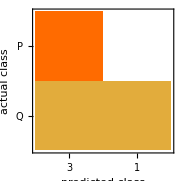
Classifier Measurements
Classifier method | DecisionTree
Number of test examples | 4
Accuracy | (75.25.) %
Accuracy baseline | (50.29.) %
Geometric mean of probabilities | 0.566 ± 0.12
Mean cross entropy | 0.569 ± 0.21
Single evaluation time | 2.67 ms/example
Batch evaluation speed | 362. examples/s
-Graphics- |

```mathematica
cm = ClassifierMeasurements[c,testset]
```

Measure accuracy and F-score and plot the confusion matrix from the ClassifierMeasurementsObjectpaclet:ref/ClassifierMeasurementsObject:

```mathematica
cm /@ {"Accuracy", "FScore", "ConfusionMatrixPlot"} // TableForm
```

0.75
<|P→0.8,Q→0.666667|>
-Graphics-

Get the properties:

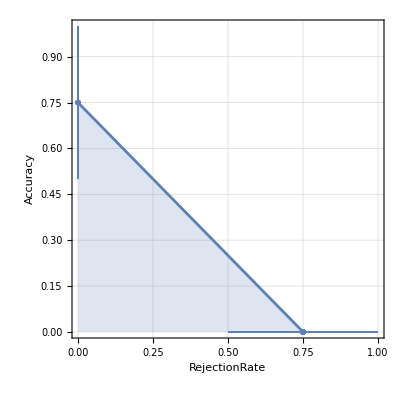
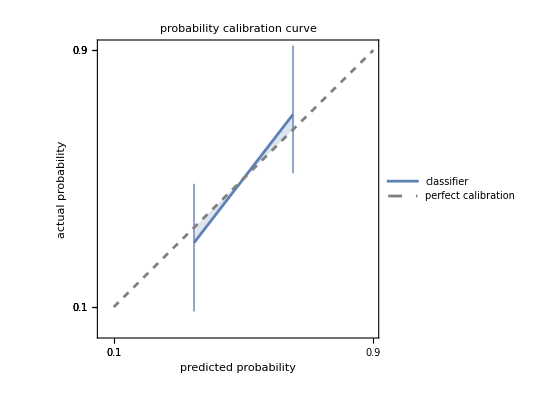
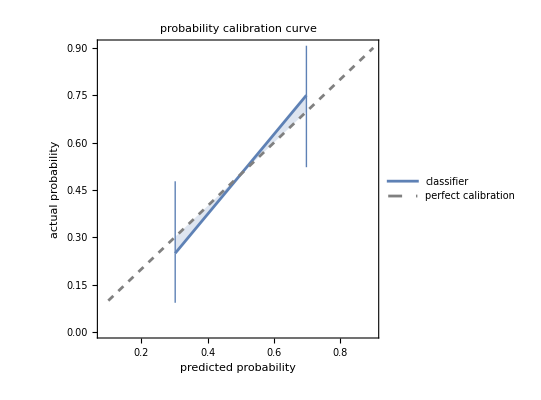
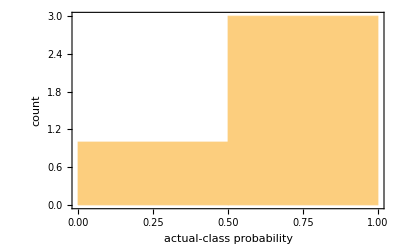
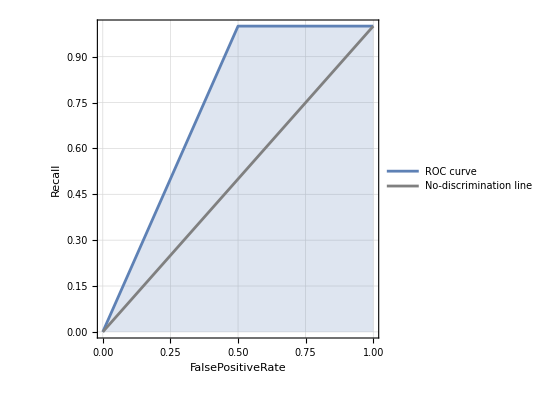
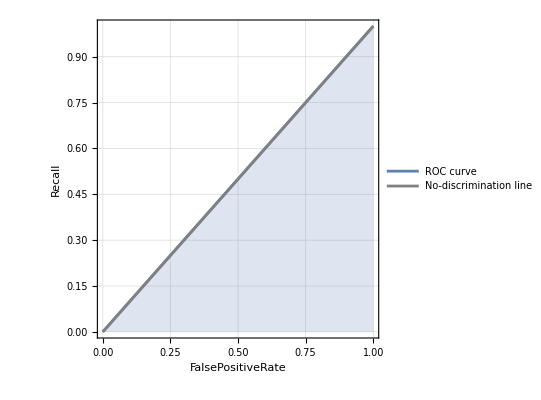
<|Accuracy→0.75,AccuracyBaseline→0.5,AccuracyRejectionPlot→-Graphics-,AreaUnderROCCurve→<|P→0.75,Q→0.5|>,BatchEvaluationTime→0.00276895,BestClassifiedExamples→{2.2→P,2.7→P,4.5→Q,1.4→Q},CalibrationCurve→-Graphics-,CalibrationData→{{0.301913507465776044,0.250.160.23},{0.698086492534224144,0.750.230.16}},ClassifierFunction→ClassifierFunction[…],ClassMeanCrossEntropy→<|P→0.359412,Q→0.778513|>,ClassRejectionRate→<|P→0.,Q→0.|>,CohenKappa→0.5,ConfusionDistribution→CategoricalDistribution[…],ConfusionFunction→<|P→<|P→2,Q→0,Indeterminate→0|>,Q→<|P→1,Q→1,Indeterminate→0|>|>,ConfusionMatrix→{{2,0,0},{1,1,0}},ConfusionMatrixPlot→-Graphics-,CorrectlyClassifiedExamples→{2.2→P,2.7→P,4.5→Q},DecisionUtilities→{1.,1.,1.,0.},Error→0.25,EvaluationTime→0.0026731,Examples→{2.2→P,2.7→P,4.5→Q,1.4→Q},F1Score→<|P→0.8,Q→0.666667|>,FalseDiscoveryRate→<|P→0.333333,Q→0.|>,FalseNegativeExamples→<|P→{},Q→{1.4→Q}|>,FalseNegativeNumber→<|P→0,Q→1|>,FalseNegativeRate→<|P→0.,Q→0.5|>,FalsePositiveExamples→<|P→{1.4→Q},Q→{}|>,FalsePositiveNumber→<|P→1,Q→0|>,FalsePositiveRate→<|P→0.5,Q→0.|>,GeometricMeanProbability→0.566112,IndeterminateExamples→{},LeastCertainExamples→{2.2→P,2.7→P,4.5→Q,1.4→Q},Likelihood→0.102709,LinearCalibrationCurve→-Graphics-,LogLikelihood→-2.27585,MatthewsCorrelationCoefficient→<|P→0.57735,Q→0.57735|>,MeanCrossEntropy→0.568963,MeanDecisionUtility→0.75,MisclassifiedExamples→{1.4→Q},MostCertainExamples→{2.2→P,2.7→P,4.5→Q,1.4→Q},NegativePredictiveValue→<|P→1.,Q→0.666667|>,Perplexity→1.76643,Precision→<|P→0.666667,Q→1.|>,Probabilities→{0.698086,0.698086,0.698086,0.301914},ProbabilityHistogram→-Graphics-,Properties→{Accuracy,AccuracyBaseline,AccuracyRejectionPlot,AreaUnderROCCurve,BatchEvaluationTime,BestClassifiedExamples,CalibrationCurve,CalibrationData,ClassifierFunction,ClassMeanCrossEntropy,ClassRejectionRate,CohenKappa,ConfusionDistribution,ConfusionFunction,ConfusionMatrix,ConfusionMatrixPlot,CorrectlyClassifiedExamples,DecisionUtilities,Error,EvaluationTime,Examples,F1Score,FalseDiscoveryRate,FalseNegativeExamples,FalseNegativeNumber,FalseNegativeRate,FalsePositiveExamples,FalsePositiveNumber,FalsePositiveRate,GeometricMeanProbability,IndeterminateExamples,LeastCertainExamples,Likelihood,LinearCalibrationCurve,LogLikelihood,MatthewsCorrelationCoefficient,MeanCrossEntropy,MeanDecisionUtility,MisclassifiedExamples,MostCertainExamples,NegativePredictiveValue,Perplexity,Precision,Probabilities,ProbabilityHistogram,Properties,Recall,RejectionRate,Report,ROCCurve,ScottPi,Specificity,TopConfusions,TrueNegativeExamples,TrueNegativeNumber,TruePositiveExamples,TruePositiveNumber,WorstClassifiedExamples},Recall→<|P→1.,Q→0.5|>,RejectionRate→0.,Report→Classifier Measurements
Classifier method | DecisionTree
Number of test examples | 4
Accuracy | (75.25.) %
Accuracy baseline | (50.29.) %
Geometric mean of probabilities | 0.566 ± 0.12
Mean cross entropy | 0.569 ± 0.21
Single evaluation time | 2.67 ms/example
Batch evaluation speed | 362. examples/s
-Graphics- | ,ROCCurve→<|P→-Graphics-,Q→-Graphics-|>,ScottPi→0.466667,Specificity→<|P→0.5,Q→1.|>,TopConfusions→{P→Q},TrueNegativeExamples→<|P→{4.5→Q},Q→{2.2→P,2.7→P}|>,TrueNegativeNumber→<|P→1,Q→2|>,TruePositiveExamples→<|P→{2.2→P,2.7→P},Q→{4.5→Q}|>,TruePositiveNumber→<|P→2,Q→1|>,WorstClassifiedExamples→{1.4→Q,2.2→P,2.7→P,4.5→Q}|>

```mathematica
PropertyAssociation[cm]
```

Create an object containing some text:

```mathematica
file=AbsoluteFileName[Export["alice.txt",ExampleData[{"Text", "AliceInWonderland"}]]];
doc=ContentObject[File[file]]
```

ContentObject[…]

Get only a snippet of the text:

```mathematica
doc["Snippet"]
```

I--DOWN THE RABBIT-HOLE Alice was beginning to get very tired of sitting by her

It is also possible to use the Snippetpaclet:ref/Snippet function:

```mathematica
Snippet[doc]
```

I--DOWN THE RABBIT-HOLE Alice was beginning to get very tired of sitting by her

Get properties of the file:

```mathematica
doc["Location"]
```

File[C:\Users\Peter\Documents\alice.txt]

```mathematica
doc["FileName"]
```

alice.txt

```mathematica
doc["FileExtension"]
```

txt

```mathematica
doc["FileSize"]
```

51.724 kB

Get the property association:

```mathematica
PropertyAssociation[doc]
```

<|CreationDate→Sat 24 Jun 2023 09:22:32GMT-4,FileByteCount→51724,FileExtension→txt,FileName→alice.txt,Location→File[C:\Users\Peter\Documents\alice.txt],ModificationDate→Sat 24 Jun 2023 09:22:32GMT-4,Plaintext→File[C:\Users\Peter\Documents\alice.txt],Title→alice|>

All does not work:

```mathematica
doc[All]
```

ContentObject[…][All]

Surprisingly, PropertyAssociation works here:

```mathematica
doc["PropertyAssociation"]
```

<|CreationDate→Sat 24 Jun 2023 09:22:32GMT-4,FileByteCount→51724,FileExtension→txt,FileName→alice.txt,Location→File[C:\Users\Peter\Documents\alice.txt],ModificationDate→Sat 24 Jun 2023 09:22:32GMT-4,Plaintext→File[C:\Users\Peter\Documents\alice.txt],Title→alice|>

Get an encrypted object by encrypting a message:

```mathematica
enc =Encrypt["my password","Now is the time..."]
```

EncryptedObject[…]

Get a property of the encrypted object:

```mathematica
enc["Data"]
```

ByteArray[…]

Get all the details contained in an EncryptedObjectpaclet:ref/EncryptedObject:

```mathematica
enc["Parameters"]
```

<|Cipher→AES256,BlockMode→CBC,InitializationVector→ByteArray[…],Data→ByteArray[…],Padding→Automatic,OriginalForm→String|>

You can also use this function:

```mathematica
PropertyAssociation[enc]
```

<|Cipher→AES256,BlockMode→CBC,InitializationVector→ByteArray[…],Data→ByteArray[…],Padding→Automatic,OriginalForm→String|>

Create an entitlement:

```mathematica
entitlement=CreateLicenseEntitlement[<|"StandardKernelLimit"->6|>]
```

LicenseEntitlementObject[…]

Access properties of the entitlement:

```mathematica
entitlement["StandardKernelLimit"]
```

6

```mathematica
entitlement["ExpirationDate"]
```

Sat 1 Jul 2023 09:33:08GMT-4

Neither All nor "PropertyAssociation" nor Information gives all the properties:

```mathematica
entitlement[All]
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[Standard|Parallel~~KernelCost][All].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[Standard|Parallel~~KernelLimit][All].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[Standard|Parallel~~KernelActiveCount][All].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

Missing[UnknownProperty,All]

```mathematica
entitlement["PropertyAssociation"]
```

Missing[UnknownProperty,PropertyAssociation]

```mathematica
Information[entitlement]
```

Information[LicenseEntitlementObject[…]]

Get every properties's value:

```mathematica
PropertyAssociation[entitlement]
```

<|CreationDate→Sat 24 Jun 2023 09:33:08GMT-4,CreditsSpent→0 credits,EntitlementID→O-WSDS-4D92-B5VLHB8XMQHCC,ExpirationDate→Sat 1 Jul 2023 09:33:08GMT-4,LicenseExpirationDuration→1 0.,ParallelKernelActiveCount→0,ParallelKernelCost→2. credits/h,ParallelKernelLimit→0,PolicyID→WSDS,PolicyName→Standard,Properties→{CreationDate,CreditsSpent,EntitlementID,ExpirationDate,LicenseExpirationDuration,ParallelKernelActiveCount,ParallelKernelCost,ParallelKernelLimit,PolicyID,PolicyName,Properties,StandardKernelActiveCount,StandardKernelCost,StandardKernelLimit},StandardKernelActiveCount→0,StandardKernelCost→2. credits/h,StandardKernelLimit→6|>

Delete the entitlement:

```mathematica
DeleteObject[entitlement]
```

Define a training set and a test set:

```mathematica
trainingset={1->2,3->4.5,5->6,7->8.5};
```

```mathematica
testset={1.5->2,4->5,6-> 5.5};
```

Create a predictor with the training set:

```mathematica
p=Predict[trainingset]
```

PredictorFunction[…]

Generate a PredictorMeasurementsObjectpaclet:ref/PredictorMeasurementsObject of the predictor with the test set:

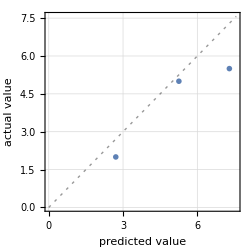
Predictor Measurements
Predictor method | LinearRegression
Number of test examples | 3
Standard deviation | 1.12 ± 0.49
Standard deviation baseline | 1.55 ± 0.4
R-squared | 0.472 ± 0.54
Mean cross entropy | 5.69 ± 4.6
Single evaluation time | 2.59 ms/example
Batch evaluation speed | 250. examples/s
-Graphics- |

```mathematica
pm=PredictorMeasurements[p, testset]
```

Measure the standard deviation and plot the residuals from the PredictorMeasurementsObjectpaclet:ref/PredictorMeasurementsObject:

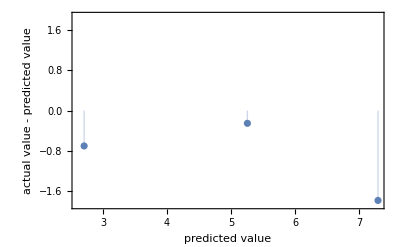
{1.12284,-Graphics-}

```mathematica
pm /@ {"StandardDeviation", "ResidualPlot"}
```

Neither All nor "PropertyAssociation" works:

```mathematica
pm[All]
```

PredictorMeasurementsObject::elmntav: All is not an available property.

Predictor Measurements
Predictor method | LinearRegression
Number of test examples | 3
Standard deviation | 1.12 ± 0.49
Standard deviation baseline | 1.55 ± 0.4
R-squared | 0.472 ± 0.54
Mean cross entropy | 5.69 ± 4.6
Single evaluation time | 2.59 ms/example
Batch evaluation speed | 250. examples/s
-Graphics- | [All]

```mathematica
pm["PropertyAssociation"]
```

PredictorMeasurementsObject::elmntav: "PropertyAssociation" is not an available property.

Predictor Measurements
Predictor method | LinearRegression
Number of test examples | 3
Standard deviation | 1.12 ± 0.49
Standard deviation baseline | 1.55 ± 0.4
R-squared | 0.472 ± 0.54
Mean cross entropy | 5.69 ± 4.6
Single evaluation time | 2.59 ms/example
Batch evaluation speed | 250. examples/s
-Graphics- | [PropertyAssociation]

Get all the data:

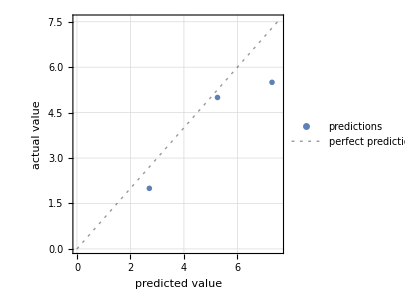
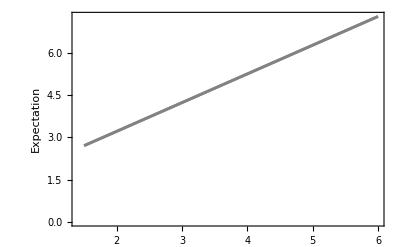
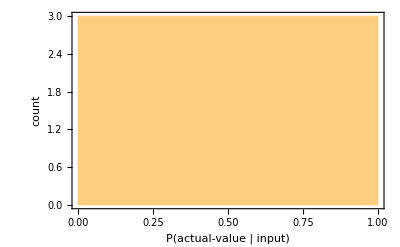
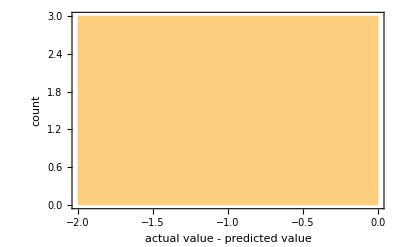
<|BatchEvaluationTime→0.00400003,BestPredictedExamples→{4→5,1.5→2,6→5.5},ComparisonPlot→-Graphics-,EvaluationTime→0.00259117,Examples→{1.5→2,4→5,6→5.5},FractionVarianceUnexplained→0.527768,GeometricMeanProbabilityDensity→0.0033768,ICEPlots→{-Graphics-},LeastCertainExamples→{1.5→2,4→5,6→5.5},Likelihood→3.85048×10^-8,LogLikelihood→-17.0725,MeanCrossEntropy→5.69083,MeanDeviation→0.918578,MeanSquare→1.26078,MostCertainExamples→{1.5→2,4→5,6→5.5},Perplexity→296.139,PredictorFunction→PredictorFunction[…],ProbabilityDensities→{0.118206,0.899673,3.62069×10^-7},ProbabilityDensityHistogram→-Graphics-,Properties→{BatchEvaluationTime,BestPredictedExamples,ComparisonPlot,EvaluationTime,Examples,FractionVarianceUnexplained,GeometricMeanProbabilityDensity,ICEPlots,LeastCertainExamples,Likelihood,LogLikelihood,MeanCrossEntropy,MeanDeviation,MeanSquare,MostCertainExamples,Perplexity,PredictorFunction,ProbabilityDensities,ProbabilityDensityHistogram,Properties,RejectionRate,Report,ResidualHistogram,ResidualPlot,Residuals,RSquared,SHAPPlots,SHAPValues,StandardDeviation,StandardDeviationBaseline,TotalSquare,WorstPredictedExamples},RejectionRate→0.,Report→Predictor Measurements
Predictor method | LinearRegression
Number of test examples | 3
Standard deviation | 1.12 ± 0.49
Standard deviation baseline | 1.55 ± 0.4
R-squared | 0.472 ± 0.54
Mean cross entropy | 5.69 ± 4.6
Single evaluation time | 2.59 ms/example
Batch evaluation speed | 250. examples/s
-Graphics- | ,ResidualHistogram→-Graphics-,ResidualPlot→-Graphics-,Residuals→{-0.706824,-0.255132,-1.79378},RSquared→0.472232,SHAPPlots→-Graphics-,SHAPValues→{-2.54318,0.00513229,2.04378},StandardDeviation→1.12284,StandardDeviationBaseline→1.5456,TotalSquare→3.78234,WorstPredictedExamples→{6→5.5,1.5→2,4→5}|>

```mathematica
PropertyAssociation[pm]
```

Use StartProcesspaclet:ref/StartProcess to start the shell process and get the corresponding ProcessObjectpaclet:ref/ProcessObject:

```mathematica
process=StartProcess[$SystemShell]
```

ProcessObject[…]

Write a command into the shell process using the corresponding ProcessObjectpaclet:ref/ProcessObject:

```mathematica
WriteLine[process,"echo display this text"];
```

Read a single line of shell output:

```mathematica
ReadLine[process]
```

Microsoft Windows [Version 10.0.19045.3086]

Neither All nor “PropertyAssociation” works:

```mathematica
process[All]
```

ProcessObject::noprop: All is not a valid property for ProcessObject

$Failed

```mathematica
process["PropertyAssociation"]
```

ProcessObject::noprop: PropertyAssociation is not a valid property for ProcessObject

$Failed

Get all the properties:

```mathematica
PropertyAssociation[process]
```

<|Program→cmd.exe,UID→4,PID→21380,PPID→7544,User→Peter,Path→C:\Windows\System32\cmd.exe,Memory→5.03808 MB,Threads→1,StartTime→Sat 24 Jun 2023 09:45:14GMT-4,UserTime→0 s,SystemTime→0.015625 s,RealTime→1 15.,Dataset→,StandardInput→OutputStream[…],StandardOutput→InputStream[…],StandardError→InputStream[…]|>

Prove a theorem in first-order logic:

```mathematica
proof=FindEquationalProof[f[f[e,e],e]==e,ForAll[a,f[a,e]==a]]
```

ProofObject[…]

Show the theorem statement:

```mathematica
proof["Theorems"]
```

f[f[e,e],e]==e

State the axioms of the theorem:

```mathematica
proof["Axioms"]
```

∀_a f[a,e]==a

Show the type of logic used:

```mathematica
proof["Logic"]
```

EquationalLogic

Show the complete list of proof steps as a Datasetpaclet:ref/Dataset object:

```mathematica
proof["ProofDataset"]
```

Show the abstract proof network:

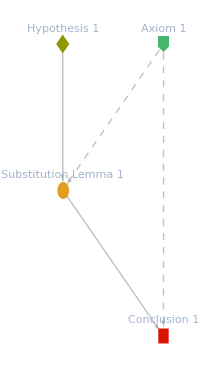

```mathematica
proof["ProofGraph"]
```

Typeset a natural language argument:

```mathematica
proof["ProofNotebook"]
```

Axiom 1
We are given that:
a==f[a,e]
Hypothesis 1
We would like to show that:
e==f[f[e,e],e]
Substitution Lemma 1
It can be shown that:
e==f[e,e]
Proof
We start by taking Hypothesis 1, and apply the substitution:
f[a_,e]→a
which follows from Axiom 1.
Conclusion 1
We obtain the conclusion:
e==e
Proof
Take Substitution Lemma 1, and apply the substitution:
f[a_,e]→a
which follows from Axiom 1.

Build a function that performs the steps of the proof:

```mathematica
pf=proof["ProofFunction"]
```

Function[{},Enclose[Block[{Axiom,Conclusion,Hypothesis,SubstitutionLemma,SubstitutionRule},Axiom_1=a_==f[a_,e];Hypothesis_1=e==f[f[e,e],e];SubstitutionRule_1=Axiom_1⟦2⟧→(Axiom_1⟦1⟧/.<|a_→a|>);SubstitutionLemma_1=ReplaceAt[Hypothesis_1,SubstitutionRule_1,{2}];ConfirmAssert[SubstitutionLemma_1===(e==f[e,e])];SubstitutionRule_2=Axiom_1⟦2⟧→(Axiom_1⟦1⟧/.<|a_→a|>);Conclusion_1=ReplaceAt[SubstitutionLemma_1,SubstitutionRule_2,{2}];ConfirmAssert[Conclusion_1===(e==e)];If[TrueQ[Activate[Conclusion_1]],Success[ProofFunction,Association[MessageTemplate→Success!]],Failure[ProofFunction,Association[MessageTemplate→Failure!]]]]]]

```mathematica
pf[]
```

Success[…]

Neither All nor “PropertyAssociation” works:

```mathematica
proof[All]
```

ProofObject[…][All]

```mathematica
proof["PropertyAssociation"]
```

ProofObject[…][PropertyAssociation]

Get all the properties:

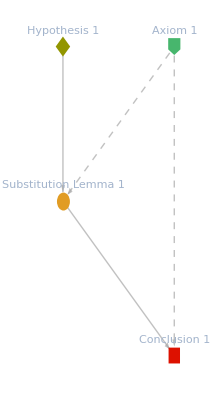
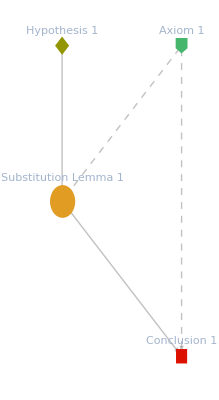
<|Axioms→∀_a f[a,e]==a,Logic→EquationalLogic,ProofDataset→,ProofFunction→Function[{},Enclose[Block[{Axiom,Conclusion,Hypothesis,SubstitutionLemma,SubstitutionRule},Axiom_1=a_==f[a_,e];Hypothesis_1=e==f[f[e,e],e];SubstitutionRule_1=Axiom_1⟦2⟧→(Axiom_1⟦1⟧/.<|a_→a|>);SubstitutionLemma_1=ReplaceAt[Hypothesis_1,SubstitutionRule_1,{2}];ConfirmAssert[SubstitutionLemma_1===(e==f[e,e])];SubstitutionRule_2=Axiom_1⟦2⟧→(Axiom_1⟦1⟧/.<|a_→a|>);Conclusion_1=ReplaceAt[SubstitutionLemma_1,SubstitutionRule_2,{2}];ConfirmAssert[Conclusion_1===(e==e)];If[TrueQ[Activate[Conclusion_1]],Success[ProofFunction,Association[MessageTemplate→Success!]],Failure[ProofFunction,Association[MessageTemplate→Failure!]]]]]],ProofGraph→-Graphics-,ProofGraphWeighted→-Graphics-,ProofLength→4,ProofNotebook→
Axiom 1
We are given that:
a==f[a,e]
Hypothesis 1
We would like to show that:
e==f[f[e,e],e]
Substitution Lemma 1
It can be shown that:
e==f[e,e]
Proof
We start by taking Hypothesis 1, and apply the substitution:
f[a_,e]→a
which follows from Axiom 1.
Conclusion 1
We obtain the conclusion:
e==e
Proof
Take Substitution Lemma 1, and apply the substitution:
f[a_,e]→a
which follows from Axiom 1.,Theorems→f[f[e,e],e]==e,Variables→{a},Constants→{}|>

```mathematica
PropertyAssociation[proof]
```

Open a connection to a server specified by a URL:

```mathematica
socket = SocketConnect["http://exampledata.wolfram.com"]
```

SocketObject[…]

Write to the socket:

```mathematica
WriteString[socket,"GET / HTTP/1.0 \n\n"]
```

Read the first line of the response:

```mathematica
Snippet[ReadLine[socket]]
```

HTTP/1.1 302 Found

Neither All nor “PropertyAssociation” works:

```mathematica
socket[All]
```

{}

```mathematica
socket["PropertyAssociation"]
```

{}

Get all the properties:

```mathematica
PropertyAssociation[socket]
```

<|ConnectedClients→None,DestinationHostname→exampledata.wolfram.com,DestinationIPAddress→IPAddress[140.177.205.136],DestinationPort→80,DirectionType→Client,InprocQ→False,Protocol→TCP,Scheme→http,SocketListener→None,Type→None,UUID→6b5b8769-7d22-49a9-a274-292fb1f4443d|>

Close the socket connection:

```mathematica
Close[socket]
```

exampledata.wolfram.com:80

Give the current SystemCredentialStoreObjectpaclet:ref/SystemCredentialStoreObject:

```mathematica
mystore=$SystemCredentialStore
```

SystemCredentialStoreObject[…]

Neither All nor “PropertyAssociation” works:

```mathematica
mystore[All]
```

SystemCredentialStoreObject[…][All]

```mathematica
mystore["PropertyAssociation"]
```

SystemCredential::unkprop: Unknown property PropertyAssociation.

$Failed

Get all the properties:

```mathematica
PropertyAssociation[mystore]
```

<|Version→1.0.0,AvailableBackends→{System,EncryptedFile},Backend→System,AvailableKeyrings→{System},Keyring→System,KeyringOpen→True,Credentials→{wolframcloudconnect:www.wolframcloud.com&burbery1@marshall.edu,ExternalEvaluateRegistry,OPENAI_API_KEY},EncryptedFileBase→Missing[NotAvailable]|>

Change the credential store:

```mathematica
$SystemCredentialStore=SystemCredentialStoreObject[<|"Backend"->"EncryptedFile","Keyring"->"System"|>]
```

SystemCredentialStoreObject[…]

Get the new properties:

```mathematica
PropertyAssociation[$SystemCredentialStore]
```

SystemCredential::unkbe: Unknown backend EncryptedFile.

General::stop: Further output of SystemCredential::unkbe will be suppressed during this calculation.

<|Version→1.0.0,AvailableBackends→{System,EncryptedFile},Backend→EncryptedFile,AvailableKeyrings→$Failed,Keyring→System,KeyringOpen→LibraryFunctionError[LIBRARY_FUNCTION_ERROR,6],Credentials→LibraryFunctionError[LIBRARY_FUNCTION_ERROR,6],EncryptedFileBase→C:\Users\Peter\AppData\Roaming\Mathematica\ApplicationData\Credentials|>

Reset the credential store to the default:

```mathematica
$SystemCredentialStore=mystore
```

SystemCredentialStoreObject[…]

Get the properties again:

```mathematica
PropertyAssociation[$SystemCredentialStore]
```

<|Version→1.0.0,AvailableBackends→{System,EncryptedFile},Backend→System,AvailableKeyrings→{System},Keyring→System,KeyringOpen→True,Credentials→{wolframcloudconnect:www.wolframcloud.com&burbery1@marshall.edu,ExternalEvaluateRegistry,OPENAI_API_KEY},EncryptedFileBase→Missing[NotAvailable]|>

Start a web session:

```mathematica
session=StartWebSession[]
```

WebSessionObject[…]

Open a webpage:

```mathematica
WebExecute[session,"OpenWebPage"->"https://en.wikipedia.org/wiki/The_Example"]
```

Success[…]

Use WebExecutepaclet:ref/WebExecute to locate a WebElementObjectpaclet:ref/WebElementObject link on a page:

```mathematica
e=RandomChoice[WebExecute[session,"LocateElements"->"Tag"->"a"]]
```

WebElementObject[…]

Use WebExecutepaclet:ref/WebExecute to find the text of a WebElementObjectpaclet:ref/WebElementObject:

```mathematica
WebExecute[session,"ElementText"->e]
```

^

Click the WebElementObjectpaclet:ref/WebElementObject link:

```mathematica
WebExecute[session,"ClickElement"->e]
```

Success[…]

Neither All nor “PropertyAssociation” works for WebElementObject or WebSessionObject:

```mathematica
session[All]
```

Missing[KeyAbsent,All]

```mathematica
session["PropertyAssociation"]
```

Missing[KeyAbsent,PropertyAssociation]

```mathematica
e[All]
```

Missing[KeyAbsent,All]

```mathematica
e["PropertyAssociation"]
```

Missing[KeyAbsent,PropertyAssociation]

Get all the properties:

```mathematica
PropertyAssociation[session]
```

<|Browser→Chrome,SessionID→42f23c94498213cfcbaa9b40cab651c5,URL→http://localhost:64124,Process→ProcessObject[…]|>

```mathematica
PropertyAssociation[e]
```

<|Browser→Chrome,SessionID→4f8ea6a0a0188d0976aaabe9cf99738f,URL→http://localhost:52023,Process→ProcessObject[…],ElementId→ACA921B8531DF3D175FBFFDB15FD0FD6_element_70|>

Close the session:

```mathematica
DeleteObject[session]
```

Start a web session:

```mathematica
session = StartWebSession[]
```

WebSessionObject[…]

Use WebExecutepaclet:ref/WebExecute to get the open window as a WebWindowObjectpaclet:ref/WebWindowObject:

```mathematica
WebExecute["BrowserWindows"]
```

{WebWindowObject[…]}

Neither All nor “PropertyAssociation” works:

```mathematica
WebWindowObject[…][All]
```

Missing[KeyAbsent,All]

```mathematica
WebWindowObject[…]["PropertyAssociation"]
```

Missing[KeyAbsent,PropertyAssociation]

Get the properties:

```mathematica
PropertyAssociation[WebWindowObject[…]]
```

<|Browser→Chrome,SessionID→630fa9f4f31ce38622ec7514e4ffe281,URL→http://localhost:55557,Process→ProcessObject[…],WindowID→C5759AF93F322CA06CBBE664FC135822|>

Delete the session with DeleteObjectpaclet:ref/DeleteObject:

```mathematica
DeleteObject[session]
```

### Properties and Relations

### Possible Issues

### Neat Examples

## Source & Additional Information

### Contributed By

Peter Burbery

### Keywords

Associations

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Repository Tools
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction
 Wolfram Physics Project |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Just For Fun
 Machine Learning
 Programming Utilities
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics

### Related Symbols

SymbolName (documented Wolfram Language symbol)

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Source/Reference Citation

Source, reference or citation information

### Links

Link to other related material

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

13.0+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about 
, issues, etc.

## Submission Notes

Additional information for the reviewer.